# Computational Analysis of the Time Dependent Schroedinger Equation

By: Andrew DeBenedictis, Anna Phillips, and Jen Radoff

## Introduction

## Importing Python-generated data

```mathematica
NotebookDirectory[]
```

C:\Users\A\Box Sync\Tufts\tims class\TDSE\GradStudentsRock_TDSE\

```mathematica
path=NotebookDirectory[];
cases={"freeParticle","squareWell","harmonicOscillator","triangle","kronigPenney","teeth","imag1","imag2","barrier1","barrier2","barrier3"};
scheme={"_SFD","_CN"};
numberType={"Real","Imag"};
periodicType={"periodic","nonPeriodic"};
eigenState = {"eValues","eVectors"};
```

## Free Particle

Let’s look at the eigenvalues and eigenvectors to start out since these are scheme-independent:

```mathematica
Clear[freeEVectorsRe,freeEVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=1;
 schemeChoice=1;
freeEValues=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["freeEVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
freeEVectors=Sqrt[freeEVectorsRe^2+freeEVectorsIm^2];
];
```

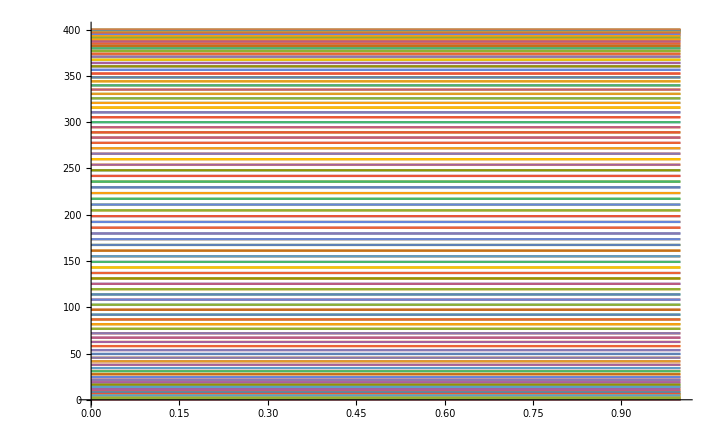

```mathematica
Plot[freeEValues,{x,0,1}]
```

```mathematica
Manipulate[ListPlot[freeEVectors⟦i,All⟧,Joined->True],{i,1,Length[freeEVectors⟦All,1⟧],1}]
```

### Scheme 1: Simple Finite Difference (SFD)

this imports in form {rows, columns} equal to {time, position}

```mathematica
Clear[freeRe,freeIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=1;
 schemeChoice=1;
Do[
Evaluate[Symbol["free"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
free=Sqrt[freeRe^2+freeIm^2];
];
```

```mathematica
Manipulate[ListPlot[{free⟦t,All⟧,freeRe⟦t,All⟧,freeIm⟦t,All⟧},PlotRange->{-.7,.7}],{t,1,Length[freeRe⟦All,1⟧],1}]
```

### Scheme 2: Crank-Nicolson (CN)

This should be the most stable scheme. For the rest of the cases, we will implement this scheme.

this imports in form {rows, columns} equal to {time, position}

```mathematica
Clear[freeNCRe,freeNCIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=1;
 schemeChoice=2;
Do[
Evaluate[Symbol["freeNC"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
freeNC=Sqrt[freeNCRe^2+freeNCIm^2];
];
```

```mathematica
Manipulate[ListPlot[{freeNC⟦t,All⟧,freeNCRe⟦t,All⟧,freeNCIm⟦t,All⟧},PlotRange->{-.7,.7}],{t,1,Length[freeNCRe⟦All,1⟧],1}]
```

#### compare the two schemes directly

```mathematica
Manipulate[ListPlot[{free⟦t,All⟧,freeNC⟦t,All⟧},PlotRange->{0,.7}],{t,1,Length[freeNCRe⟦All,1⟧],1}]
```

#### and check normalization

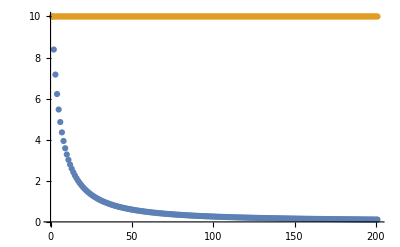

```mathematica
ListPlot[{Total[free^2,{2}],Total[freeNC^2,{2}]}]
```

Scheme 2 doesn’t lose normalization!

### Scheme 2 with non-Periodic boundary conditions

```mathematica
Clear[freeNonPeriodicNCRe,freeNonPeriodicNCIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["freeNonPeriodicNC"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
freeNonPeriodicNC=Sqrt[freeNonPeriodicNCRe^2+freeNonPeriodicNCIm^2];
];
```

```mathematica
Manipulate[ListPlot[{freeNonPeriodicNC⟦t,All⟧,freeNonPeriodicNCRe⟦t,All⟧,freeNonPeriodicNCIm⟦t,All⟧},PlotRange->{-.7,.7}],{t,1,Length[freeNonPeriodicNCRe⟦All,1⟧],1}]
```

PINBALL!!!!

## Square Well

Non-periodic

## Harmonic Oscillator

Non-periodic

## Triangle

Non-periodic

## Kronig-Penney

Periodic

## Barrier

Non-periodic. Grid size is large compared to barrier width.

### Height = E

### Height < E

### Height > E

## V=ix

Non-periodic

## V=x+ix

Non-periodic

## Discussion?

About the non-Hermitian-ness...